```mathematica
Subscript[z, max]:= 1/ω √(2ϵ);
Subscript[z, min]:= 0;
Subscript[j, z]:= 2/π √(2ϵ -ω^2*z^2);
Integrate[Subscript[j, z],{z,Subscript[z, min],Subscript[z, max]}]
```

ϵ/ω

```mathematica
FullSimplify[%7]
```

```mathematica
Simplify[%10]
```

ϵ/ω

```mathematica
Plot3D[ϵ/ω,{ϵ,-8,8},{ω,-8,8}]
```

-Graphics3D-

```mathematica
Subscript[z, max]:= 1/ω √(2ϵ);
```

```mathematica
∫_0^Subscript[z, max] 2/π √(2ϵ -ω^2*z^2) ⅆz
```

ϵ/ω

```mathematica
D[ϵ/ω, ω]
```

-ϵ/ω^2

```mathematica
Subscript[ρ, min]:= 1/ω(ϵ-√(ϵ^2-ω^2*m^2))^(1/2);
Subscript[ρ, max]:= 1/ω(ϵ+√(ϵ^2-ω^2*m^2))^(1/2);
Subscript[j, ρ]:= √(2 ϵ- ω^2*ρ^2-m^2/ρ^2);
Integrate[Subscript[j, ρ],{ρ, Subscript[ρ, min], Subscript[ρ, max]}]
```

∫_((√(ϵ-√(ϵ^2-m^2 ω^2)))/ω)^((√(ϵ+√(ϵ^2-m^2 ω^2)))/ω) √(2 ϵ-m^2/ρ^2-ρ^2 ω^2)ⅆρ

```mathematica
f[ρ_]:=ρ+1/ρ^2;
```

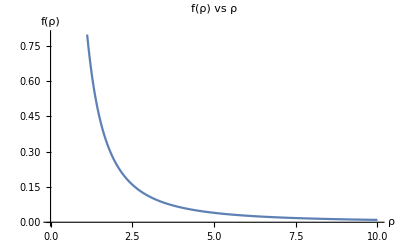

```mathematica
Plot[f[ρ],{ρ,0,10},AxesLabel->{"ρ","f(ρ)"},PlotLabel->"f(ρ) vs ρ"]
```

```mathematica
f[x_]:= ∫1/x √(2 ϵ x -ω^2 x^2-m^2)ⅆx 
Evaluate[f[x]]
```

√(-m^2+2 x ϵ-x^2 ω^2)+(ⅈ ϵ Log[(2 ⅈ ϵ)/ω-2 ⅈ x ω+2 √(-m^2+2 x ϵ-x^2 ω^2)])/ω+ⅈ m Log[(2 ⅈ m^2-2 ⅈ x ϵ-2 m √(-m^2+2 x ϵ-x^2 ω^2))/(m^3 x)]

```mathematica
p=ρ^2;
Simplify[√(-m^2+2 x ϵ-x^2 ω^2)+(ⅈ ϵ Log[(2 ⅈ ϵ)/ω-2 ⅈ x ω+2 √(-m^2+2 x ϵ-x^2 ω^2)])/ω+ⅈ m Log[(2 ⅈ m^2-2 ⅈ x ϵ-2 m √(-m^2+2 x ϵ-x^2 ω^2))/(m^3 x)]/.x->p ]
```

√(-m^2+2 ϵ ρ^2-ρ^4 ω^2)+(ⅈ ϵ Log[(2 ⅈ ϵ)/ω-2 ⅈ ρ^2 ω+2 √(-m^2+2 ϵ ρ^2-ρ^4 ω^2)])/ω+ⅈ m Log[(2 ⅈ (m^2-ϵ ρ^2+ⅈ m √(-m^2+2 ϵ ρ^2-ρ^4 ω^2)))/(m^3 ρ^2)]

```mathematica
Subscript[p, 1]:= 1/ω(ϵ+√(ϵ^2-ω^2*m^2))^(1/2);
Subscript[p, 2]:= 1/ω(ϵ-√(ϵ^2-ω^2*m^2))^(1/2);
Simplify[√(-m^2+2 ϵ ρ^2-ρ^4 ω^2)+(ⅈ ϵ Log[(2 ⅈ ϵ)/ω-2 ⅈ ρ^2 ω+2 √(-m^2+2 ϵ ρ^2-ρ^4 ω^2)])/ω+ⅈ m Log[(2 ⅈ (m^2-ϵ ρ^2+ⅈ m √(-m^2+2 ϵ ρ^2-ρ^4 ω^2)))/(m^3 ρ^2)]/.ρ->Subscript[p, 1]-√(-m^2+2 ϵ ρ^2-ρ^4 ω^2)+(ⅈ ϵ Log[(2 ⅈ ϵ)/ω-2 ⅈ ρ^2 ω+2 √(-m^2+2 ϵ ρ^2-ρ^4 ω^2)])/ω+ⅈ m Log[(2 ⅈ (m^2-ϵ ρ^2+ⅈ m √(-m^2+2 ϵ ρ^2-ρ^4 ω^2)))/(m^3 ρ^2)]/.ρ->Subscript[p, 2]]
```

1/ω(ω √(-1/ω^2(m^2 ω^2+(√(ϵ+√(ϵ^2-m^2 ω^2))+ⅈ ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+ⅈ m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^4+2 ϵ (-ⅈ √(ϵ+√(ϵ^2-m^2 ω^2))+ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^2))+ⅈ ϵ Log[1/ω 2 (-ⅈ √(ϵ^2-m^2 ω^2)+2 ϵ √(ϵ+√(ϵ^2-m^2 ω^2)) Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+ⅈ ϵ^2 Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]^2+2 m ω √(ϵ+√(ϵ^2-m^2 ω^2)) Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]+2 ⅈ m ϵ ω Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω] Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]+ⅈ m^2 ω^2 Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]^2+ω √(-1/ω^2(m^2 ω^2+(√(ϵ+√(ϵ^2-m^2 ω^2))+ⅈ ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+ⅈ m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^4+2 ϵ (-ⅈ √(ϵ+√(ϵ^2-m^2 ω^2))+ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^2)))]+ⅈ m ω Log[(2 (ⅈ ϵ^2-ⅈ m^2 ω^2+ⅈ ϵ √(ϵ^2-m^2 ω^2)-2 ϵ^2 √(ϵ+√(ϵ^2-m^2 ω^2)) Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]-ⅈ ϵ^3 Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]^2-2 m ϵ ω √(ϵ+√(ϵ^2-m^2 ω^2)) Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]-2 ⅈ m ϵ^2 ω Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω] Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]-ⅈ m^2 ϵ ω^2 Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]^2+m ω^2 √(-1/ω^2(m^2 ω^2+(√(ϵ+√(ϵ^2-m^2 ω^2))+ⅈ ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+ⅈ m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^4+2 ϵ (-ⅈ √(ϵ+√(ϵ^2-m^2 ω^2))+ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^2))))/(m^3 (-ⅈ √(ϵ+√(ϵ^2-m^2 ω^2))+ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^2)])

```mathematica
∑_(m=1)^∞ %9
```

∑_(m=1)^∞ 1/ω(ω √(-1/ω^2(m^2 ω^2+(√(ϵ+√(ϵ^2-m^2 ω^2))+ⅈ ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+ⅈ m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^4+2 ϵ (-ⅈ √(ϵ+√(ϵ^2-m^2 ω^2))+ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^2))+ⅈ ϵ Log[1/ω 2 (-ⅈ √(ϵ^2-m^2 ω^2)+2 ϵ √(ϵ+√(ϵ^2-m^2 ω^2)) Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+ⅈ ϵ^2 Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]^2+2 m ω √(ϵ+√(ϵ^2-m^2 ω^2)) Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]+2 ⅈ m ϵ ω Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω] Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]+ⅈ m^2 ω^2 Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]^2+ω √(-1/ω^2(m^2 ω^2+(√(ϵ+√(ϵ^2-m^2 ω^2))+ⅈ ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+ⅈ m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^4+2 ϵ (-ⅈ √(ϵ+√(ϵ^2-m^2 ω^2))+ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^2)))]+ⅈ m ω Log[(2 (ⅈ ϵ^2-ⅈ m^2 ω^2+ⅈ ϵ √(ϵ^2-m^2 ω^2)-2 ϵ^2 √(ϵ+√(ϵ^2-m^2 ω^2)) Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]-ⅈ ϵ^3 Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]^2-2 m ϵ ω √(ϵ+√(ϵ^2-m^2 ω^2)) Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]-2 ⅈ m ϵ^2 ω Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω] Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]-ⅈ m^2 ϵ ω^2 Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]^2+m ω^2 √(-1/ω^2(m^2 ω^2+(√(ϵ+√(ϵ^2-m^2 ω^2))+ⅈ ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+ⅈ m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^4+2 ϵ (-ⅈ √(ϵ+√(ϵ^2-m^2 ω^2))+ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^2))))/(m^3 (-ⅈ √(ϵ+√(ϵ^2-m^2 ω^2))+ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^2)])

```mathematica
Simplify[%10]
```

∑_(m=1)^∞ 1/ω(ω √(-1/ω^2(m^2 ω^2+(√(ϵ+√(ϵ^2-m^2 ω^2))+ⅈ ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+ⅈ m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^4+2 ϵ (-ⅈ √(ϵ+√(ϵ^2-m^2 ω^2))+ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^2))+ⅈ ϵ Log[1/ω 2 (-ⅈ √(ϵ^2-m^2 ω^2)+2 ϵ √(ϵ+√(ϵ^2-m^2 ω^2)) Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+ⅈ ϵ^2 Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]^2+2 m ω √(ϵ+√(ϵ^2-m^2 ω^2)) Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]+2 ⅈ m ϵ ω Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω] Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]+ⅈ m^2 ω^2 Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]^2+ω √(-1/ω^2(m^2 ω^2+(√(ϵ+√(ϵ^2-m^2 ω^2))+ⅈ ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+ⅈ m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^4+2 ϵ (-ⅈ √(ϵ+√(ϵ^2-m^2 ω^2))+ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^2)))]+ⅈ m ω Log[(2 (ⅈ ϵ^2-ⅈ m^2 ω^2+ⅈ ϵ √(ϵ^2-m^2 ω^2)-2 ϵ^2 √(ϵ+√(ϵ^2-m^2 ω^2)) Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]-ⅈ ϵ^3 Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]^2-2 m ϵ ω √(ϵ+√(ϵ^2-m^2 ω^2)) Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]-2 ⅈ m ϵ^2 ω Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω] Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]-ⅈ m^2 ϵ ω^2 Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]^2+m ω^2 √(-1/ω^2(m^2 ω^2+(√(ϵ+√(ϵ^2-m^2 ω^2))+ⅈ ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+ⅈ m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^4+2 ϵ (-ⅈ √(ϵ+√(ϵ^2-m^2 ω^2))+ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^2))))/(m^3 (-ⅈ √(ϵ+√(ϵ^2-m^2 ω^2))+ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^2)])

```mathematica
Simplify[%9]
```

1/ω(ω √(-1/ω^2(m^2 ω^2+(√(ϵ+√(ϵ^2-m^2 ω^2))+ⅈ ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+ⅈ m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^4+2 ϵ (-ⅈ √(ϵ+√(ϵ^2-m^2 ω^2))+ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^2))+ⅈ ϵ Log[1/ω 2 (-ⅈ √(ϵ^2-m^2 ω^2)+2 ϵ √(ϵ+√(ϵ^2-m^2 ω^2)) Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+ⅈ ϵ^2 Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]^2+2 m ω √(ϵ+√(ϵ^2-m^2 ω^2)) Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]+2 ⅈ m ϵ ω Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω] Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]+ⅈ m^2 ω^2 Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]^2+ω √(-1/ω^2(m^2 ω^2+(√(ϵ+√(ϵ^2-m^2 ω^2))+ⅈ ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+ⅈ m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^4+2 ϵ (-ⅈ √(ϵ+√(ϵ^2-m^2 ω^2))+ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^2)))]+ⅈ m ω Log[(2 (ⅈ ϵ^2-ⅈ m^2 ω^2+ⅈ ϵ √(ϵ^2-m^2 ω^2)-2 ϵ^2 √(ϵ+√(ϵ^2-m^2 ω^2)) Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]-ⅈ ϵ^3 Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]^2-2 m ϵ ω √(ϵ+√(ϵ^2-m^2 ω^2)) Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]-2 ⅈ m ϵ^2 ω Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω] Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]-ⅈ m^2 ϵ ω^2 Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))]^2+m ω^2 √(-1/ω^2(m^2 ω^2+(√(ϵ+√(ϵ^2-m^2 ω^2))+ⅈ ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+ⅈ m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^4+2 ϵ (-ⅈ √(ϵ+√(ϵ^2-m^2 ω^2))+ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^2))))/(m^3 (-ⅈ √(ϵ+√(ϵ^2-m^2 ω^2))+ϵ Log[(2 ⅈ √(ϵ^2-m^2 ω^2))/ω]+m ω Log[-(2 ⅈ (-ϵ^2+m^2 ω^2+ϵ √(ϵ^2-m^2 ω^2)))/(m^3 (-ϵ+√(ϵ^2-m^2 ω^2)))])^2)])